Momentum is not a good quantum number for qc, therefore one expects the local density of states |Ω(k,E)|^2 not to be diagonal.
Where Ω(k,E) = Σ_E'|ψ_k(E')|^2 δ(E'-E).
However it has an interesting structure, as Rolof, Thiem and Schreiber point out (Eur. Phys. J. B (2013) 86: 372).

```mathematica
ω=N [(Sqrt[5]-1)/2];
(* with this choice the chain is palindromic except when n=3m+1 *)
r=28;
fib[n_]:=IntegerPart[ω( n+1+r)]-IntegerPart[ω(n+r)];
jump[n_,ρ_]:=If[fib[n-1]<1,1.,ρ];
```

```mathematica
jump[#,ρ]&/@Range[Fibonacci[7]-1]
```

{1.,ρ,ρ,1.,ρ,ρ,1.,ρ,1.,ρ,ρ,1.}

```mathematica
Clear[h];
h[n_,ρ_]:=Block[{L=Fibonacci[n],tbl,ar},
tbl=Table[{i,i+1}->jump[i,ρ],{i,1,L-1}];
(* periodic boundary conditions *)
AppendTo[tbl,{1,L}->ρ];
ar=SparseArray[tbl,{L,L}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
ft[list_]:=Block[{n=Length[list]},Table[1/(√n)∑_(r=1)^n list[[r]] ⅇ^(2π ⅈ(r-1-n/2)(s-1)/n),{s,1,n}]];
```

```mathematica
(* Fourier transform of the wavefunctions *)
{en,{wf,wfk}}=Block[{n=11,ρ=0.5,val,vec,o,veck},
{val,vec}=Eigensystem[h[n,ρ]];
o=Ordering[val];
vec=vec[[o]];
val=val[[o]];
veck=ParallelMap[Fourier,vec];
{val,{vec,veck}}
];
```

```mathematica
Length[en]/2.
```

44.5

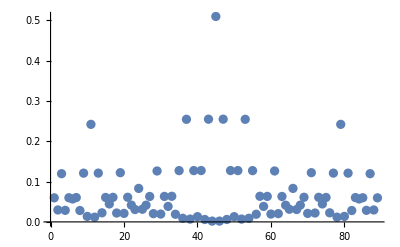

```mathematica
i=45;
ListPlot[Abs[wf[[i]]],PlotRange->All]
```

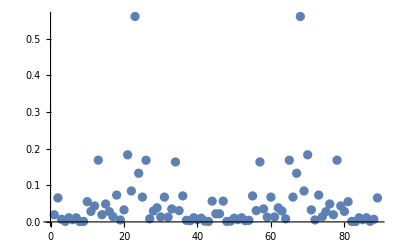

```mathematica
i=45;
ListPlot[Abs[wfk[[i]]],PlotRange->All]
```

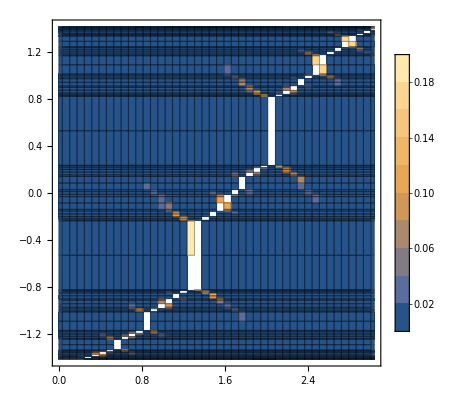

```mathematica
L=Length[wfk];
Ω=Transpose[wfk][[IntegerPart[L/2];;L]];
Ω=Abs[Transpose[Ω]]^2//Chop;
klist=N[Range[0,Pi,2Pi/L]];
Ω=Flatten[Table[{klist[[k]],en[[e]],Ω[[e,k]]},{e,L},{k,IntegerPart[L/2]}],1];
ListContourPlot[Ω,InterpolationOrder->0,PlotLegends->Automatic,PlotRange->{0,.2},Mesh->All]
```